```mathematica
DualDiagram[λ_] := Total /@ Transpose[
     (PadRight[#1, λ[[1]]] & ) /@ 
      (ConstantArray[1, #1] & ) /@ λ]; 
ToYD[stb_]:=Length/@stb;
CheckStandard[λT_] := 
   And @@ Flatten[{Table[λT[[a - 1,s]] < 
        λT[[a,s]], {a, 2, Length[λT]}, 
       {s, 1, Length[λT[[a]]]}], 
      Table[λT[[a,s - 1]] < λT[[a,s]], 
       {a, 1, Length[λT]}, {s, 2, 
        Length[λT[[a]]]}], Sort[Flatten[λT]] == 
       Range[Length[Flatten[λT]]], 
      ListQ /@ λT}]; 
ToTableau[path_]:=Block[{pr=path//Flatten,max},max=Max[pr];
Table[Position[pr,k]//Flatten,{k,max}]];
Quiet[Needs["Combinatorica`"]];
ToSYT[rigged_]:=ToTableau[kkrrec[ConstantArray[{1,1},Length[rigged[[1,1]]]],rigged[[2;;3]]]];
```

```mathematica
(*Importing a Matlab package allowing us to plot rigged configurations*)
Directory[];
SetDirectory["C:\\Users\\thoma\\OneDrive\\Dokument\\Uppsala\\Fysik\\Project_Bethe_ansatz\\VolinStringHypothesis\\StringHypothesis"];
<<RC.m;
ResetDirectory[];
```

```mathematica
ModestoRiggedConfig[L_,modes_]:=Module[{Mmatrix,limits},
Mmatrix=PadRight[Append[Prepend[Table[Length[modes[[i,j]]],{i,Length[modes]},{j,Length[modes[[i]]]}],SparseArray[1->L,1]],{0}]];
limits=(Delete[-Cartan[Length[Mmatrix]].Mmatrix.Kernel[Length[Mmatrix[[1]]]],{{1},{-1}}]+Delete[Mmatrix/.{0->{}},{{1},{-1}}])/2-1/2;
Prepend[Append[{}]/@(Table[{Table[ConstantArray[i,Length[modes[[j,i]]]],{i,Sort[Range[Length[modes[[j]]]],Greater]}]//Catenate,Table[limits[[j,i]]+modes[[j,i,k]]+1-k,{i,Sort[Range[Length[modes[[j]]]],Greater]},{k,Length[modes[[j,i]]]}]//Map[Sort[#,Greater]&,#]&//Catenate},{j,Length[modes]}]//Transpose),{ConstantArray[1,L]}]
]

RiggedToModes[rigged_]:=Module[{L,strings,riggings,r,sMax,MrowLens,firstRow,lastRow,Mmatrix,holes,limits,modes},L=Length[rigged[[1,1]]];
strings=rigged[[2]];
riggings=rigged[[3]];
r=Length[strings];
sMax=Max@Flatten[strings/. {}->0];
MrowLens=Table[Count[strings[[a]],s],{a,r},{s,sMax}];
firstRow=ConstantArray[0,sMax];
firstRow[[1]]=L;
lastRow=ConstantArray[0,sMax];
Mmatrix=PadRight@Join[{firstRow},MrowLens,{lastRow}];
holes=-Cartan[Length[Mmatrix]].Mmatrix.Kernel[sMax];
limits=((Delete[holes,{{1},{-1}}]+MrowLens)/2)-1/2;
modes=Table[Module[{occ=ConstantArray[0,sMax],rowModes=Table[{},{s,sMax}]},Do[With[{s=strings[[a,n]]},occ[[s]]++;
AppendTo[rowModes[[s]],riggings[[a,n]]-limits[[a,s]]-1+occ[[s]]]],{n,Length[strings[[a]]]}];
Reverse[rowModes]],{a,r}];
modes=Select[modes,AnyTrue[#,(#=!={})&]&];
modes=Map[Reverse,modes];
modes];
```

```mathematica
Fsym[x_,-1,0]:=(1/Pi)ArcTan[x];
MM[a_,s_,YD_]:=MM[a,s,YD]=Total[YD]+a s-Total[YD[[1;;a]]]-Total[DualDiagram[YD][[1;;s]]];
YQa[0,0,YD_]:=u^Total[YD]+Sum[u^(Total[YD]-k)sym[k],{k,Total[YD]}];
YQa[a_,s_,YD_]:=u^MM[a,s,YD]+Sum[c[a,s,k] u^(MM[a,s,YD]-k),{k,MM[a,s,YD]}];
YQaθ[a_,s_,YD_]:=Product[u-qθ[a,s,k],{k,1,MM[a,s,YD]}]/.qθ[0,0,n_]:>θ[n];
QQrel[a_,s_,YD_]:=
CoefficientList[(YQa[a,s,YD]/.u->u+I/2)(YQa[a+1,s+1,YD]/.u->u-I/2)-(YQa[a,s,YD]/.u->u-I/2)(YQa[a+1,s+1,YD]/.u->u+I/2)-I(MM[a,s,YD]-MM[a+1,s+1,YD])YQa[a+1,s,YD]YQa[a,s+1,YD],u]//(#/.Complex[0,b_]:>b)&;
```

```mathematica
coeff2root[YD_]:=Table[If[{a,s}!={0,0},Thread[CoefficientList[YQa[a,s,YD],u][[;;-2]]->CoefficientList[YQprod[a,s,YD],u][[;;-2]]],Nothing],{a,0,Length[YD]-1},{s,0,YD[[a+1]]-1}]//Flatten;
rootsfromcoeff[YD_,sol_]:=Block[{k},Table[If[{a,s}!={0,0},k=1;ReplaceAll[#,u->x[a,s,k++]]&/@(NSolve[YQa[a,s,YD]/.sol,u]//Flatten),Nothing],{a,0,Length[YD]-1},{s,0,YD[[a+1]]-1}]//Flatten];
```

```mathematica
Strings2Roots[strings_]:=Flatten/@Map[Table[#[[2]]-I/2*(#[[1,2]]-1-2k),{k,0,#[[1,2]]-1}]&,GatherBy[strings,#[[1,1]]&],{2}]
```

```mathematica
Q[x_,n_]:=If[x===0&&n===0,1,(x+n I)/(x-n I)]
```

```mathematica
GenerateθSystem[stringtypes_,L_]:=(BAEθ[k_,a_,s_]:=If[a==1,Product[Q[v[a,s,k]-θ[i],s/2],{i,L}],Product[Q[(v[a,s,k]-v[a-1,ss,jj]),nn],{ss,1,Length[stringtypes[[a-1]]]},{jj,1,Length[stringtypes[[a-1,ss]]]},{nn,(s-ss)/2+1/2,(s+ss)/2-1/2}]]*If[a==Length[stringtypes],1,Product[Q[(v[a,s,k]-v[a+1,ss,jj]),nn],{ss,1,Length[stringtypes[[a+1]]]},{jj,1,Length[stringtypes[[a+1,ss]]]},{nn,(s-ss)/2+1/2,(s+ss)/2-1/2}]]+twist[a]Product[Q[2(v[a,s,k]-v[a,ss,jj]),s-ss]*Q[2(v[a,s,k]-v[a,ss,jj]),(s+ss)]*Product[Q[(v[a,s,k]-v[a,ss,jj]),nn],{nn,(s-ss)/2+1,(s+ss)/2-1}]^2,{ss,1,Length[stringtypes[[a]]]},{jj,1,Length[stringtypes[[a,ss]]]}];
Allrelsθ=(Table[BAEθ[k,a,s],{a,1,Length[stringtypes]},{s,1,Length[stringtypes[[a]]]},{k,1,Length[stringtypes[[a,s]]]}]//Flatten)/.θ[i_]:>If[i==1,Λ,0];
vars=Table[v[a,s,k],{a,1,Length[stringtypes]},{s,1,Length[stringtypes[[a]]]},{k,1,Length[stringtypes[[a,s]]]}]//Flatten;

(*Linear approximations used for predictor*)
J=D[Allrelsθ,{vars}];
fdot=D[Allrelsθ,Λ];)
```

```mathematica
Exactrels[yd_]:=Table[(YQaθ[a,0,yd]/.u->u+I)/(YQaθ[a,0,yd]/.u->u-I)+(YQaθ[a-1,0,yd]/.u->u+I/2)/(YQaθ[a-1,0,yd]/.u->u-I/2) (YQaθ[a+1,0,yd]/.u->u+I/2)/(YQaθ[a+1,0,yd]/.u->u-I/2)/.Table[{u->qθ[a,0,i]},{i,MM[a,0,yd]}],{a,1,Length[yd]-1}]/.θ[i_]:>If[i==1,Λ,0]//Flatten
```

```mathematica
(*Linear predictor*)
stringpredθ[solLast_,ΛLast_,dΛ_]:=Thread[(solLast//Keys)->(solLast//Values)+(LinearSolve[J/.solLast/.Λ->ΛLast,-fdot/.solLast/.Λ->ΛLast])*dΛ];
```

```mathematica
(*Newton corrector*)
stringfinderθ[Λ0_,predictor_]:=(minsolrep=FindRoot[Allrelsθ/.Λ->Rationalize[Λ0],{vars,vars/.predictor}//Transpose,WorkingPrecision->prec,PrecisionGoal->prec,AccuracyGoal->prec/2,MaxIterations->∞];);
```

```mathematica
Iterateθ:=Block[{},
Λvals={Λstart};
ΛLast=Λvals[[-1]];

n=0;
Monitor[While[ΛLast<Λtarget,(*step=Rationalize[step*E^(n/10)];n++;*)
Λnew=Min[ΛLast+step,Λtarget];

prednew=stringpredθ[solθ[ΛLast],ΛLast,Min[step,Λtarget-ΛLast]];

stringfinderθ[Λnew,prednew];
solθ[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
ΛLast=Λvals[[-1]]],
Row@{"Current Λ: ",Λvals[[-1]]//N," current step: ",step//N}];
];
```

The code demands as input “sol[1]”, which is a string solution for a rigged configuration.

For now, I have specified “rigged” but one can skip this and specify mode numbers, “modes”, directly of course. The mode numbers encode the values M_a^(s), which are used to define the equation system.

The code also demands “yd”, which is the Young diagramme of this rigged configuration (for convenience of coding, this is asked for separately.)

These inputs are described in commented text below.

inputs

```mathematica
(*Choice of yd as input. rigged config or modes as input (otherwise, rigged config is converted to modes using RiggedToModes.*)
yd={4,2,1};
rigged={{{1,1,1,1,1,1,1}},{{2,1},{1},{}},{{0,1},{0},{}}};
modes=(rigged//RiggedToModes);

(*sol[1] is a string solution for the relevant rigging in the form {v[a,s,k]->n,...} where v[a,s,k] is the centre of the kth string at level a with length s.*)

(*SolutionFromModeConfiguration[modes,L];*)(*A function I use to find string solutions for a given set of mode numbers*)

solθ[Λstart]=sol[1];
```

converting inputs to proper form

```mathematica
L=Total[yd];
(*Defines the start, stop and steps of the iteration in Λ.*)
Λstart=0;
Λtarget=30;
step=0.1;

(*The iteration demands a list of numbers of strings of different lengthts. So, stringyptes={{2,1},{1}} means that at level 1, there are 2 strings of length 1 and 1 string of length 2; at level 2 there is 1 string of length 1. For now, stringtypes is defined using modes (which is the reason these were defined above).*)
stringtypes=Table[Table[ConstantArray[i,Length[modes[[j,i]]]],{i,Sort[Range[Length[modes[[j]]]],Greater]}]//Catenate,{j,Length[modes]}];

(*One can add twists to the equations; set to zero for now.*)
Do[twist[i]=Exp[Rationalize[I i RandomReal[{-1,1}0],0.001]],{i,Length[stringtypes]}]
```

the iteration

```mathematica
(*The actual iteration; demands stringtypes, L, solθ[Λstart]. The iteration produces three lists: Λlist, Λstringlist and Λrootlist.*)
GenerateθSystem[Gather/@Sort/@stringtypes,L]
Iterateθ
{Λlist,Λstringlist,Λrootlist}=stringAtθ={Λvals,solθ[#]&/@Λvals,Strings2Roots[solθ[#]]&/@Λvals};
```

looking at the data

```mathematica
(*For convenience, the original rigged config and the next one according to KKR is printed.*)
Map[Sort,-modes,{2}]//ModestoRiggedConfig[L,#]&//showRC
(newrigged=((Map[Sort,-modes,{2}]//ModestoRiggedConfig[L,#]&//ToSYT)/.L->Nothing/.{}->Nothing)//ToRigged[#,Length[#]]&)//showRC
newmodes=newrigged//RiggedToModes;
```

-Graphics- | -Graphics- | ∅

-Graphics- | -Graphics- | ∅

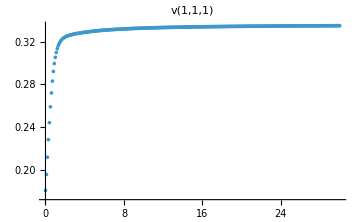
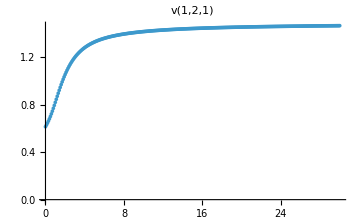

```mathematica
(*Plotting centres of strings at different levels.*)
level=1;
levelvars=Select[vars,#[[1]]==level&];
Table[ListPlot[{Λlist,levelvars[[i]]/.Λstringlist//Chop}//Transpose,PlotRange->All,PlotLabel->levelvars[[i]],ImageSize->Medium],{i,Length[levelvars]}]
```